# Клеточные автоматы

```mathematica
BaseForm[30,2]
```

11110_2

#### Правила преобразования на трехбитовых участках регистра

Правило может быть закодировано номером: 
верхняя строка - последовательность всех трехбитовых комбинаций, нижняя - результат преобразования

```mathematica
{RulePlot[CellularAutomaton[{110,2}]],BaseForm[110,2]}
```

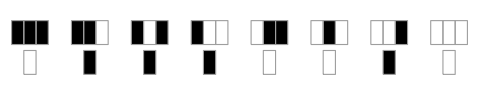
{-Graphics-,1101110_2}

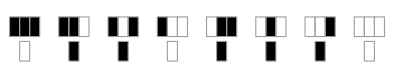
{-Graphics-,1101110_2}

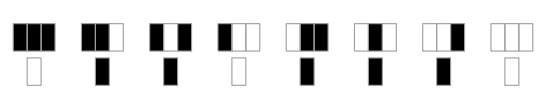
{-Graphics-,1101110_2}

```mathematica
{RulePlot[CellularAutomaton[{114,2}]],BaseForm[110,2]}
```

Результат 4 - х применений правила

```mathematica
CellularAutomaton[110,{{1,0,1,0,0,1,1,0,1,0,1,0,0,0},0},4]//Grid
```

0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1

#### Последовательность состояний в виде графика

Правило - 30 (00111110), начальное состояние - 0001000, количество итераций - 32

```mathematica
ArrayPlot[CellularAutomaton[30,{0,0,0,1,0,0,0},32]]
```

-Graphics-

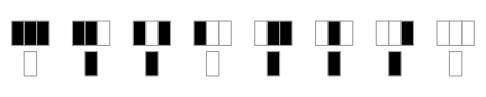
-Graphics- | 1101110_2 | 110

```mathematica
Table[{RulePlot[CellularAutomaton[{i,2}]],BaseForm[i,2],i},{i,110,110}] // TableForm
```

#### Применение правила n раз на неграниченном массиве

```mathematica
ArrayPlot[CellularAutomaton[110,{{1},0},2^7]]
```

-Graphics-

### Различные клеточные автоматы, 50 итераций

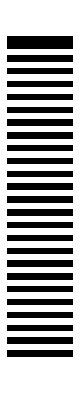
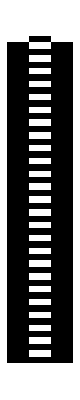
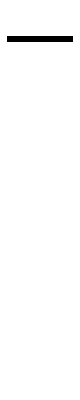
{{-Graphics-,110},{-Graphics-,111},{-Graphics-,112},{-Graphics-,113},{-Graphics-,114},{-Graphics-,115},{-Graphics-,116},{-Graphics-,117},{-Graphics-,118},{-Graphics-,119},{-Graphics-,120},{-Graphics-,121},{-Graphics-,122},{-Graphics-,123},{-Graphics-,124},{-Graphics-,125},{-Graphics-,126},{-Graphics-,127},{-Graphics-,128}}

```mathematica
Table[{ArrayPlot[CellularAutomaton[i,{{1},0},50]],i},{i,110,128}]
```

#### Эволюция автомата 1599

```mathematica
Row[Table[ArrayPlot[CellularAutomaton[{1599,{3,1}},{{1},0},{{t,t+200}}],ImageSize->{Automatic,200}],{t,0,600,200}]]
```

-Graphics--Graphics--Graphics--Graphics-

### Двумерные клеточные автоматы

```mathematica
Manipulate[ArrayPlot[CellularAutomaton[<|"Dimension"->2,"OuterTotalisticCode"->746|>,{{Table[1,7]},0},{{{i}}}]],{i,1,288,1}]
```

```mathematica
Graphics3D[Cuboid/@Position[#,1],ImageSize->Tiny]&/@CellularAutomaton[{126, {2, 1}, {1, 1,1}},{{{{1}}},0},10]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

#### Игра "Жизнь"

```mathematica
ArrayPlot[#,ImageSize->40,Mesh->True]&/@CellularAutomaton["GameOfLife",{{{0,1,0},{0,0,1},{1,1,1}},0},8]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Manipulate[Image[CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{SeedRandom[1];RandomInteger[1,{15,15}],0},n] ,ImageSize-> {320,320}],{n,0,500,1}]
```

```mathematica
Manipulate[Image3D[CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{SeedRandom[1];RandomInteger[1,{16,16}],0},n] ,ImageSize-> {320,320}],{n,0,500,1}]
```